## Release Notes

challenge1-2 : Add in a constant term to the fits. 
challenge1-1 : Periodogram to find periods (PMC.m extended to eliminate dead Gaussians)

## Setup

```mathematica
(* Initialize stuff *)
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Needs["PMC`"];
Needs["GLSTools`"];
```

## Data

```mathematica
(* Read in data *)
vrad =SemanticImport["vrad_simu_challenge_inclination_90_1.rdb",ExcludedLines->{2}];
```

```mathematica
Keys[vrad][[1]]//Normal
```

{jdb,rv,sig_rv,fwhm,sig_fwhm,bis_span,sig_bis_span,rhk,sig_rhk,rv_osc_and_gran,rv_activity,rv_planet,rv_inst_noise,fwhm_osc_and_gran,fwhm_activity,fwhm_inst_noise,bis_span_osc_and_gran,bis_span_activity,bis_span_inst_noise,rhk_osc_and_gran,rhk_activity,rhk_inst_noise}

```mathematica
(* Extract columns we want *)
```

```mathematica
data = Normal@vrad[All,#]&/@ {"jdb",1000(#"rv_planet"+#"rv_inst_noise")&,1/(1000 #"sig_rv")^2&};
```

```mathematica
Clear[plot1];
plot1[logP_]:=ListPlot[Transpose[{FractionalPart[data[[1]]/Exp[logP]],data[[2]]}]]
```

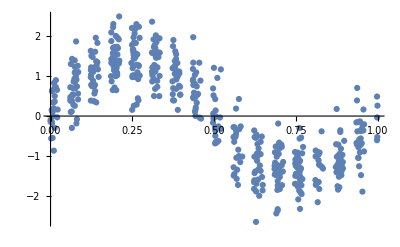

```mathematica
plot1[Log[16]]
```

```mathematica
(* Work out fundamental frequency, standard deviation, max time *)
tmax = Max@data[[1]] - Min@data[[1]];
ffreq = 2 Pi/Max@data[[1]];
sddata = StandardDeviation[data[[2]]];
sdslope = sddata/tmax;
mdata = Mean@data[[2]];
```

## Simple periodogram

```mathematica
freqs = Range[ffreq,0.5,ffreq]; (* Arbitrary cutoff at half a day *)
pgram=GLS[data[[1]],data[[2]], data[[3]], freqs];
pfap = FAP[data[[1]],data[[2]], data[[3]],freqs,50];
```

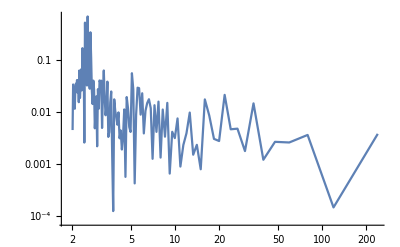

```mathematica
ListLogLogPlot[Transpose[{1/freqs,pgram}],Joined->True,PlotRange->Full]
```

```mathematica
Quantile[pfap,0.95]
```

0.0119921

```mathematica
1/freqs[[10;;20]]
```

{23.8747,21.7042,19.8956,18.3651,17.0533,15.9164,14.9217,14.0439,13.2637,12.5656,11.9373}

```mathematica
pgram[[10;;20]]
```

{0.00466939,0.0214768,0.00277718,0.00305159,0.00860102,0.017559,0.000793214,0.00234411,0.00151114,0.00980222,0.00391546}

```mathematica
trials = Select[Transpose[{freqs,pgram}],#[[2]]>Quantile[pfap,0.95]&];
Length@trials
```

60

## Model

```mathematica
Clear[rvmodel,chi2];
rvmodel[phi_,lfreq_,logK_,c0_]:=Module[{f,K=Exp[logK]},
f = 2 Pi (FractionalPart[data[[1]]Exp[lfreq]]+phi);
K Cos[f]+c0
]
chi2[phi_?NumericQ,lfreq_?NumericQ,logK_?NumericQ,c0_?NumericQ]:=Module[{rv},
rv = rvmodel[phi,lfreq,logK,c0];
Total[(data[[2]]- rv)^2*data[[3]]]
]
```

## Refinement

```mathematica
mins=NMinimize[{chi2[p,l,k,c0],p≥0,p<1},{{p,0,1},{l,Log[0.8 #],Log[1.2 #]},{k,-5,5},{c0,mdata-sddata,mdata+sddata}},PrecisionGoal->2,AccuracyGoal->1]&/@trials[[All,2]]
```

{{1223.5,{p→0.755006,l→-2.72968,k→0.197707,c0→0.0641473}},{2600.52,{p→5.86338×10^-13,l→-3.56618,k→-0.8294,c0→0.051005}},{1223.5,{p→0.755007,l→-2.72968,k→0.197715,c0→0.0641478}},{2594.01,{p→0.930111,l→-3.56401,k→-0.827175,c0→0.0531468}},{464.322,{p→0.74482,l→-2.7725,k→0.396876,c0→0.00864144}},{2600.52,{p→4.35124×10^-11,l→-3.56618,k→-0.8294,c0→0.051005}},{2594.01,{p→0.930112,l→-3.56401,k→-0.827177,c0→0.0531468}},{1228.78,{p→0.744087,l→-2.81731,k→0.226315,c0→-0.0207829}},{1228.78,{p→0.744086,l→-2.81731,k→0.22632,c0→-0.0207835}},{464.322,{p→0.744819,l→-2.7725,k→0.396877,c0→0.00864114}},{1223.5,{p→0.755007,l→-2.72968,k→0.197715,c0→0.0641477}},{1881.47,{p→5.86338×10^-13,l→-2.8213,k→-0.0591671,c0→0.0572551}},{464.322,{p→0.74482,l→-2.7725,k→0.396874,c0→0.00864157}},{2575.63,{p→1.91118×10^-10,l→-3.47353,k→-0.759071,c0→0.0281325}},{2575.63,{p→1.17584×10^-8,l→-3.47353,k→-0.759071,c0→0.0281324}},{1228.78,{p→0.744086,l→-2.81731,k→0.22632,c0→-0.0207834}},{2575.63,{p→2.70345×10^-9,l→-3.47353,k→-0.759071,c0→0.0281323}},{464.322,{p→0.74482,l→-2.7725,k→0.396875,c0→0.00864143}},{464.322,{p→0.744817,l→-2.7725,k→0.39688,c0→0.00864078}},{2564.91,{p→0.909499,l→-3.47082,k→-0.743424,c0→0.0353111}},{464.322,{p→0.74482,l→-2.7725,k→0.396874,c0→0.00864155}},{464.322,{p→0.74482,l→-2.7725,k→0.396874,c0→0.00864153}},{1223.5,{p→0.755007,l→-2.72968,k→0.197714,c0→0.0641478}},{1228.78,{p→0.744086,l→-2.81731,k→0.226321,c0→-0.0207834}},{464.322,{p→0.74482,l→-2.7725,k→0.396877,c0→0.00864083}},{464.322,{p→0.744818,l→-2.7725,k→0.396877,c0→0.00864116}},{1881.47,{p→8.27842×10^-12,l→-2.8213,k→-0.059167,c0→0.0572552}},{464.322,{p→0.744819,l→-2.7725,k→0.396869,c0→0.00864539}},{2564.91,{p→0.909497,l→-3.47082,k→-0.743422,c0→0.0353111}},{464.322,{p→0.74482,l→-2.7725,k→0.396875,c0→0.0086415}},{2630.97,{p→0.885961,l→-2.88917,k→-0.939422,c0→0.0723162}},{2564.91,{p→0.909499,l→-3.47082,k→-0.743424,c0→0.0353111}},{464.322,{p→0.744819,l→-2.7725,k→0.396875,c0→0.00864141}},{2693.29,{p→0.438789,l→-0.110262,k→-1.23331,c0→0.0912583}},{464.322,{p→0.744819,l→-2.7725,k→0.396879,c0→0.00864113}},{464.322,{p→0.74482,l→-2.7725,k→0.396876,c0→0.00864143}},{464.322,{p→0.74482,l→-2.7725,k→0.396874,c0→0.00864173}},{1704.68,{p→0.649118,l→0.0657503,k→0.0341037,c0→0.0809543}},{464.322,{p→0.74482,l→-2.7725,k→0.396874,c0→0.00864155}},{464.322,{p→0.74482,l→-2.7725,k→0.396875,c0→0.00864141}},{464.322,{p→0.744817,l→-2.7725,k→0.39688,c0→0.00864115}},{2710.82,{p→0.239381,l→-0.105493,k→-1.30292,c0→0.0967589}},{2602.38,{p→0.624905,l→-2.33721,k→-0.849413,c0→0.0897104}},{464.322,{p→0.74482,l→-2.7725,k→0.396874,c0→0.00864161}},{2579.11,{p→0.0994953,l→-3.02019,k→-0.738066,c0→0.0981552}},{2579.11,{p→0.0994953,l→-3.02019,k→-0.738066,c0→0.0981552}},{464.322,{p→0.744817,l→-2.7725,k→0.396878,c0→0.00864102}},{464.322,{p→0.744818,l→-2.7725,k→0.396877,c0→0.00864118}},{2594.01,{p→0.930112,l→-3.56401,k→-0.827177,c0→0.0531468}},{464.322,{p→0.74482,l→-2.7725,k→0.396874,c0→0.00864157}},{2575.63,{p→1.18681×10^-12,l→-3.47353,k→-0.759071,c0→0.0281323}},{464.322,{p→0.74482,l→-2.7725,k→0.396875,c0→0.0086415}},{2564.91,{p→0.909499,l→-3.47082,k→-0.743424,c0→0.0353111}},{464.322,{p→0.74482,l→-2.7725,k→0.396875,c0→0.00864149}},{2575.63,{p→1.15452×10^-12,l→-3.47353,k→-0.759071,c0→0.0281324}},{464.322,{p→0.744816,l→-2.7725,k→0.396874,c0→0.00864372}},{1223.5,{p→0.755007,l→-2.72968,k→0.197714,c0→0.0641478}},{1228.78,{p→0.744086,l→-2.81731,k→0.226317,c0→-0.020783}},{464.322,{p→0.74482,l→-2.7725,k→0.396875,c0→0.00864146}},{1228.78,{p→0.744087,l→-2.81731,k→0.226315,c0→-0.0207828}}}

## PMC

### Initialize

```mathematica
npop=10000;
mix = {1,{p,l,k,c0}/.#,DiagonalMatrix[{0.1,0.1,0.3,sddata/2}]} &/@ mins[[All,2]];
model= buildModels@mix;
eps = DiagonalMatrix[{0.01,0.001,0.01,0.001}^2];
Clear[fiddle];
fiddle[x_,y_,z_,c0_] := {Mod[x,1],y,z,c0};
fiddle[-0.9,10,10,0]
```

{0.1,10,10,0}

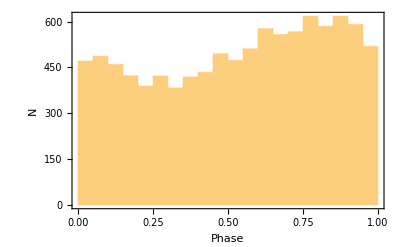

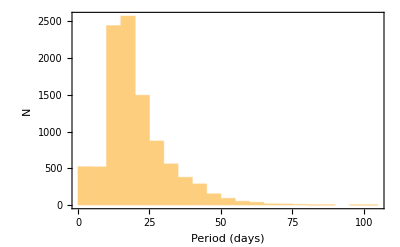

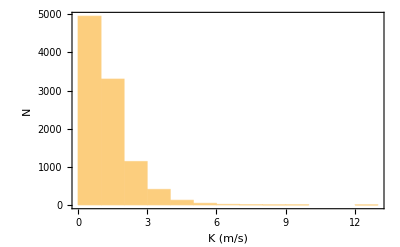

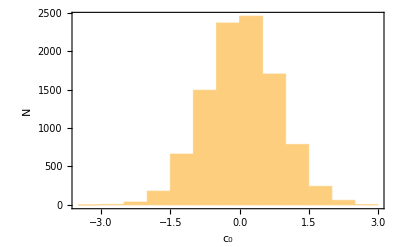

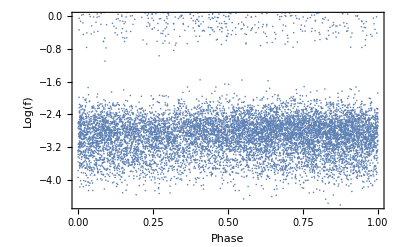

```mathematica
xx = mkRandom[model,npop, fiddle]; (* One off for simplicity *)
Histogram[xx[[All,1]],Frame->True,Axes->False,FrameLabel->{"Phase","N"}]
Histogram[Exp[-xx[[All,2]]],Frame->True,Axes->False,FrameLabel->{"Period (days)","N"}]
Histogram[Exp[xx[[All,3]]],Frame->True,Axes->False,FrameLabel->{"K (m/s)","N"}]
Histogram[xx[[All,4]],Frame->True,Axes->False,FrameLabel->{"c_0","N"}]
(*Histogram[xx[[All,5]],Frame->True,Axes->False,FrameLabel->{"c_1","N"}]*)
ListPlot[xx[[All,{1,2}]],Frame->True,Axes->False,FrameLabel->{"Phase","Log(f)"}]
```

### Loop

```mathematica
{perplex,xx,model}=iterPMC[chi2,npop,model,eps,fiddle,100];
```

Iteration:0 0.0001 {0.724093,-2.77221,0.35709,0.0453547}

Number of components:57

Iteration:1 0.00735654 {0.739925,-2.77244,0.368422,0.0455674}

Number of components:57

Iteration:2 0.0118007 {0.744019,-2.77245,0.383371,0.0471738}

Number of components:57

Iteration:3 0.0443971 {0.743712,-2.77249,0.391119,0.0438181}

Number of components:57

Iteration:4 0.000494305 {0.75068,-2.77254,0.40444,0.0210133}

Number of components:57

Iteration:5 0.0412406 {0.74394,-2.77249,0.399125,0.0195725}

Number of components:57

Iteration:6 0.0900868 {0.744386,-2.7725,0.396108,0.0127074}

Number of components:57

Iteration:7 0.146352 {0.744856,-2.7725,0.39554,0.00890695}

Number of components:57

Iteration:8 0.168151 {0.744924,-2.7725,0.395457,0.00693723}

Number of components:57

Iteration:9 0.193302 {0.744875,-2.7725,0.395445,0.00895682}

Number of components:57

Iteration:10 0.210351 {0.745132,-2.77251,0.396296,0.00977169}

Number of components:57

Iteration:11 0.225471 {0.744737,-2.7725,0.395921,0.00814924}

Number of components:57

Iteration:12 0.251207 {0.744898,-2.7725,0.395936,0.00824156}

Number of components:57

Iteration:13 0.268501 {0.744692,-2.7725,0.395352,0.00848479}

Number of components:57

Iteration:14 0.300627 {0.744769,-2.7725,0.396345,0.00815266}

Number of components:57

Iteration:15 0.327226 {0.74478,-2.7725,0.395658,0.00909647}

Number of components:57

Iteration:16 0.355776 {0.744767,-2.7725,0.395826,0.00951463}

Number of components:57

Iteration:17 0.392245 {0.744843,-2.7725,0.395406,0.00878417}

Number of components:57

Iteration:18 0.415675 {0.744842,-2.7725,0.395742,0.00856909}

Number of components:57

Iteration:19 0.458397 {0.745125,-2.77251,0.396131,0.00798568}

Number of components:57

Iteration:20 0.486114 {0.745104,-2.7725,0.395324,0.00910357}

Number of components:57

Iteration:21 0.53207 {0.745096,-2.7725,0.395886,0.00888281}

Number of components:57

Iteration:22 0.565038 {0.744797,-2.7725,0.396545,0.00811955}

Number of components:57

Iteration:23 0.604543 {0.745011,-2.7725,0.395785,0.00864612}

Number of components:57

Iteration:24 0.641313 {0.745035,-2.7725,0.395747,0.00908901}

Number of components:57

Iteration:25 0.680459 {0.744644,-2.7725,0.395878,0.00875158}

Number of components:57

Iteration:26 0.722049 {0.744898,-2.7725,0.395984,0.00874903}

Number of components:57

Iteration:27 0.758525 {0.744817,-2.7725,0.395681,0.00890428}

Number of components:57

Iteration:28 0.790368 {0.744727,-2.7725,0.395851,0.00852295}

Number of components:57

Iteration:29 0.82368 {0.744847,-2.7725,0.396103,0.00843459}

Number of components:57

Iteration:30 0.853013 {0.744902,-2.7725,0.395585,0.00931864}

Number of components:57

Iteration:31 0.874937 {0.744768,-2.7725,0.396231,0.00869996}

Number of components:57

Iteration:32 0.903435 {0.744972,-2.7725,0.395762,0.00860235}

Number of components:57

Iteration:33 0.917953 {0.744732,-2.7725,0.395956,0.00881971}

Number of components:57

Iteration:34 0.937944 {0.744745,-2.7725,0.395797,0.00872856}

Number of components:57

Iteration:35 0.95435 {0.744829,-2.7725,0.395718,0.00899476}

Number of components:57

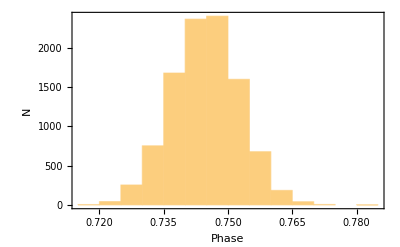

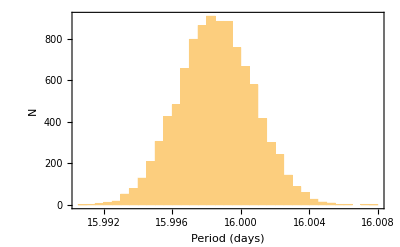

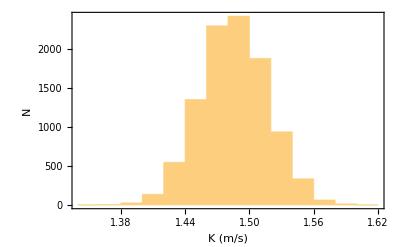

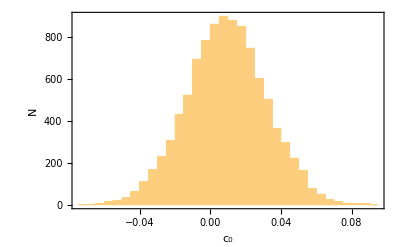

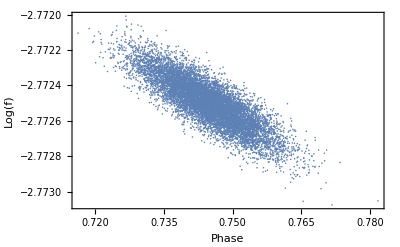

```mathematica
Histogram[xx[[All,1]],Frame->True,Axes->False,FrameLabel->{"Phase","N"}]
Histogram[Exp[-xx[[All,2]]],Frame->True,Axes->False,FrameLabel->{"Period (days)","N"}]
Histogram[Exp[xx[[All,3]]],Frame->True,Axes->False,FrameLabel->{"K (m/s)","N"}]
Histogram[xx[[All,4]],Frame->True,Axes->False,FrameLabel->{"c_0","N"}]
(*Histogram[xx[[All,5]],Frame->True,Axes->False,FrameLabel->{"c_1","N"}]*)
ListPlot[xx[[All,{1,2}]],Frame->True,Axes->False,FrameLabel->{"Phase","Log(f)"}]
```